# Quantum Algorithms for Real-World Applications

## Installing Other Libraries in Mathematica

If you have used only built-in Mathematica functions, you may not be used to installation of libraries. However, community members create a variety of convenient paclets, and you can run code from other programming languages written by your collaborators.

In this workshop, you will see extensive use of Classiq's library for quantum algorithms.

Note that ExternalEvaluate and related functions are unsupported in the public cloud. So you will need to download this notebook in order to use all of the features you will see in this workshop.

Installing this library can be done using the code below and takes several minutes if you don’t already have all the dependencies:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

PacletObject[…]

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`QuantumOptimization`
```

```mathematica
classiq=ClassiqSetup[{"Session","ClassiqVersion"},"CheckDependencies"->{"pyomo","scikit-learn"},"InstallPackages"->{"scikit-learn"}]
```

Installing latest Classiq version

```mathematica
session=classiq["Session"]
```

ExternalSessionObject[…]

#### Register an Account with Classiq

First link doesn’t work.
Mads: revised

In order to authenticate with the Classiq servers, you will need to follow Classiq's registration instructions, and be logged in to https://platform.classiq.io.

This takes less than five minutes. Much of Classiq’s library can be used without registration. However, the circuit synthesis and state vector simulation for a very large circuit will require this registration and authentication step.

from classiq import authenticate
authenticate()

Is this supposed to be here?
Mads: yes, OK

Your user code: FQKM-PVWX

If a browser doesn't automatically open, please visit this URL from any trusted device: https://auth.classiq.io/activate?user_code=FQKM-PVWX

## Modeling an HHL Algorithm to Solve a Set of Linear Equations

Guidance for the workshop: The # TODO is there for you to do yourself. The # Solution start and # Solution end are only for helping you. Try doing it yourself…

Solving linear equations appears in many research, engineering and design fields. For example, many physical and financial models, from fluid dynamics to portfolio optimization, are described by partial differential equations, which are typically treated by numerical schemes, most of which are eventually transformed to a set of linear equations.

The HHL algorithm is a quantum algorithm for solving a set of linear equations. It is one of the fundamental quantum algorithms that is expected to give a speedup over its classical counterpart.

A set of linear equations of size  is represented by an  matrix and a vector  of size , , where the solution to the problem is designated by the solution variable .

For simplicity, the demo below treats a use case where  is a normalized vector , and  is an Hermitian matrix of size  whose eigenvalues are in the interval . Generalizations to other use cases are discussed at the end of this demo.

## Defining a Specific Problem

Start by defining the specific problem. For the sake of this workshop, let’s define the initial matrices in Python:

import numpy as np
import scipy as scipy

A = np.array(
    [
        [0.28, -0.01, 0.02, -0.1],
        [-0.01, 0.5, -0.22, -0.07],
        [0.02, -0.22, 0.43, -0.05],
        [-0.1, -0.07, -0.05, 0.42],
    ]
)

b = np.array([1, 2, 4, 3])
b = b / np.linalg.norm(b)
num_qubits = int(np.log2(len(b)))

[A,b]

{NumericArray[…],NumericArray[…]}

Now that we have those array outputs, let’s save them to Wolfram Language symbols:

```mathematica
{A,b}=%
```

{NumericArray[…],NumericArray[…]}

For convenience, let’s also have these arrays in normal form:

```mathematica
{Amat,bvec}={Normal@A,Normal@b};
MatrixForm/@{Amat,bvec}
```

{(0.28 | -0.01 | 0.02 | -0.1
-0.01 | 0.5 | -0.22 | -0.07
0.02 | -0.22 | 0.43 | -0.05
-0.1 | -0.07 | -0.05 | 0.42),(0.182574
0.365148
0.730297
0.547723)}

For this particular example to work, it must be the case that  is Hermitian and has eigenvalues in the interval .

You can check this as follows, as in Classiq’s documentation:

if not np.allclose(A, A.conj().T, rtol=1e-6, atol=1e-6):
    raise Exception("The matrix is not symmetric")
w, v = np.linalg.eig(A)
for lam in w:
    if lam < 0 or lam > 1:
        raise Exception("Eigenvalues are not in (0,1)")

sol_classical = np.linalg.solve(A, b)
print("Classical solution: x = ", sol_classical)

Classical solution: x =  [1.3814374  2.50585064 3.19890483 2.43147877]

Or as follows in Wolfram Language:

```mathematica
HermitianMatrixQ[Amat]
```

True

```mathematica
AllTrue[Eigenvalues[Amat],λ|->0<λ<1]
```

True

```mathematica
xclassical=LinearSolve[Amat,bvec]
```

{1.38144,2.50585,3.1989,2.43148}

## Building a Simple HHL with Classiq

### Define the Model

You have only listed three steps.
Mads: revised

This tutorial gives instructions on building an HHL algorithm and presents the theory of the algorithm. The algorithm consists of the following steps:

1) State preparation of the RHS vector 
2) QPE for the unitary matrix , which encodes eigenvalues on a quantum register of size 
3) An inversion algorithm that loads amplitudes according to the inverse of the eigenvalue registers

#### State Preparation for the Vector b⃗

The first stage of the HHL algorithm is to load the normalized RHS vector  into a quantum register:

where  are states in the computational basis.

Comments:

• The relevant built-in function is the prepare_amplitudes one, which gets  values of , as well as an upper bound for its functional error through the bound parameter:

from classiq import *


@qfunc
def load_b(b: CArray[CReal], res: Output[QNum]) -> None:
    # TODO prepare the state |b> in the "res" register - the amplitude of res states correspond to the values of the vector b
    # Solution start
    prepare_amplitudes(b, 0.0, res)
    # Solution end

ExternalFunction[…]

This should be divided into three cells, but it won’t let me do it.
Mads: revised

Let's see the loading of b in a state vector simulator.

Update the qmod to have aer_simulator_statevector as backend, with one shot.

Refer to Execution preferences documentation and to Classiq backends documentation.

Note: This code will open a new browser window for you. You will also need have signed in to the Classiq platform on your browser to correctly see the circuit. (This can be done through a Google account or similar sign in as well.):

@qfunc
def main(res: Output[QNum]):
    load_b(b.tolist(), res)


from classiq import *
from classiq.execution import ClassiqBackendPreferences, ExecutionPreferences
from classiq.synthesis import set_execution_preferences

qmod_b_load = create_model(main)
# TODO update the qmod to have aer_simulator_statevector as backend, with one shot

# Solution start
backend_preferences = ClassiqBackendPreferences(backend_name="simulator_statevector")
qmod_b_load = set_execution_preferences(
    qmod_b_load,
    execution_preferences=ExecutionPreferences(
        num_shots=1, backend_preferences=backend_preferences
    ),
)
# Solution end
qprog_b_load = synthesize(qmod_b_load)
show(qprog_b_load)

Quantum program link: https://platform.classiq.io/circuit/36woeqSzNKlkiOkeb7hrnzRLSG9

-Graphics-

Take a look at the resulting circuit. Now let’s execute and see if b⃗ was built correctly:

job = execute(qprog_b_load)
job.open_in_ide()

-Graphics-

Let’s also see what the transpiled circuit looks like in the Wolfram Quantum Framework (make sure you have followed the installation step if you have not done so once before):

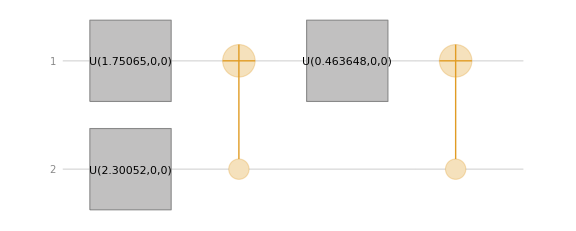

```mathematica
bLoad=With[{qasm=ExternalEvaluate[session,"qprog_b_load.transpiled_circuit.qasm"]},
ImportQASMCircuit[qasm]["QuantumCircuit"]
];
bLoad["Diagram",ImageSize->Large]
```

Check if you see the relationship between the original b⃗ and the resulting state vector:

```mathematica
bLoad[]["Amplitudes"]
```

<|00→0.182574,01→0.730297,10→0.365148,11→0.547723|>

```mathematica
bvec
```

{0.182574,0.365148,0.730297,0.547723}

Note the components of b⃗ are encoded in the amplitudes of the resulting quantum state. There can be some swapping of qubit labels, depending on your numbering convention:

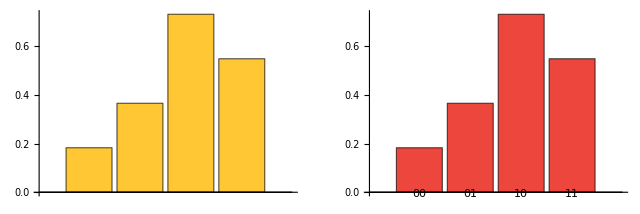

```mathematica
With[{qc=QuantumCircuitOperator[{bLoad,"SWAP"->{1,2}}]},
Labeled[
GraphicsRow[{BarChart[bvec],qc[]["AmplitudesPlot"]}],
Style["b⃗ vs swapped amplitudes","Text"],Top]
]
```

#### Quantum Phase Estimation (QPE) for the Hamiltonian Evolution U=ⅇ^(2π ⅈ A)

The QPE function block, which is at the heart of the HHL algorithm, operates as follows: Unitary matrices have eigenvalues of norm 1 and thus are of the form , with . For a quantum state , prepared in an eigenvalue of some unitary matrix  of size , the QPE algorithm encodes the corresponding eigenvalue into a quantum register:

where  is the precision of the binary representation of ,  with  being the state of the ^th qubit.

In the HHL algorithm, a QPE for the unitary  is applied. The mathematics: First, note that the eigenvectors of  are the ones of the matrix , and that the corresponding eigenvalues  defined for  are the eigenvalues of . Second, represent the prepared state in the basis given by the eigenvalues of . This is merely a mathematical transformation, with no algorithmic considerations here. If the eigenbasis of  is given by the set , then

Applying the QPE stage gives

Comments:

• Use the built-in qpe function.

Later on we see how to call qpe, but for now, here is what this circuit looks like:

-Graphics-

#### Eigenvalue Inversion

The next step in the HHL algorithm is to pass the inverse of the eigenvalue registers into their amplitudes, using the Amplitude Loading (AL) construct.

Given a function , it implements . For the HHL algorithm, apply an AL with , where  is a lower bound for the minimal eigenvalue of .

Applying this AL gives

where  is a normalization coefficient.

lower-> lowest?
Mads: revised

The normalization coefficient , which guarantees that the amplitudes are normalized, can be taken as the lowest possible eigenvalue that can be resolved with the QPE:

The built-in construct to define an amplitude loading is designated by *=; see Expression Assignment Operations. Let’s try to load together some amplitude into a qubit. Choose your own function and fill in:

@qfunc
def main(x: Output[QNum[4, UNSIGNED, 4]], ind: Output[QBit]) -> None:
    allocate(x)
    hadamard_transform(x)
    allocate(ind)
    # Solution start
    assign_amplitude_table(lookup_table(lambda x: x**2, x), x, ind)
    # Solution end
    
amplitude_loading_example_qmod = create_model(main)
amplitude_loading_example_qprog = synthesize(amplitude_loading_example_qmod)
show(amplitude_loading_example_qprog)
job_ale = execute(amplitude_loading_example_qprog)
job_ale.open_in_ide()

Quantum program link: https://platform.classiq.io/circuit/36wohLlhkMmHaFUtALiw418lDVw

-Graphics-

-Graphics-

So loading the inverse of the amplitude will be done using:

@qfunc
def simple_eig_inv(phase: Const[QNum], indicator: Output[QBit]):
    # TODO allocate 1 qubit for indicator
    # TODO load its |1> state amplitude to be C/phase using the assign_amplitude_table function

    # Solution start
    allocate(indicator)
    assign_amplitude_table(
        lookup_table(lambda p: 0 if p == 0 else (1 / 2**phase.size) / p, phase),
        phase,
        indicator,
    )
    # Solution end

ExternalFunction[…]

#### Inverse QPE

As the final step in the HHL model, clean the QPE register by applying an inverse QPE. (Note that it is not guaranteed that this register is completely cleaned; namely, that all the qubits in the QPE register return to zero after the inverse QPE. Generically they are all zero with very high probability.)

In this model, we will simply call the QPE function with the same parameters in stage 2. This is what the quantum state looks like now:

The state entangled with  stores the solution to our problem (up to some normalization problem):

#### Putting It All Together

Again, this cell won’t let me divide it.
Mads: revised

Let's remind ourselves that the entire HHL algorithm is composed of:

1) State preparation of the RHS vector .
2) QPE for the unitary matrix , which encodes eigenvalues on a quantum register of size .
3) An inversion algorithm that loads amplitudes according to the inverse of the eigenvalue registers.
4) An inverse QPE with the parameters in (2).

And put all together in my_hhl function.

You can apply QPE† EigenValInv QPE using the within_apply operator:

@qfunc
def my_hhl(
    fraction_digits: int,
    b: CArray[CReal],
    unitary_with_matrix: QCallable[QArray],
    res: Output[QArray],
    phase: Output[QNum],
    indicator: Output[QBit],
) -> None:
    # TODO Call load_b you created, to load "b" vector into register "res"
    # Solution start
    load_b(b, res)
    # Solution end

    # TODO allocate a qnum register for "phase". This qnum should be in the range [0,1) with fraction_digits precision
    # Solution start
    allocate(fraction_digits, False, fraction_digits, phase)
    # Solution end

    # TODO refer to applying (QPE†)*(EigenValInv)*(QPE) : we want to apply "simple_eig_inv" within "qpe"
    # Solution start
    within_apply(
        lambda: qpe(unitary=lambda: unitary_with_matrix(res), phase=phase),
        lambda: simple_eig_inv(phase=phase, indicator=indicator),
    )
    # Solution end

ExternalFunction[…]

Cell won’t divide.
Mads: revised

The first entry point of any model would be the main function.

Since you already have done the job in my_hhl function, all we have to do now is to call it with the relevant inputs.

Call my_hhl with QPE_SIZE digits resolution, on the normalized b, where the unitary is based on unitary_mat:

QPE_SIZE = 4


@qfunc
def main(res: Output[QNum], phase: Output[QNum], indicator: Output[QBit]):
    b_normalized = b.tolist()
    unitary_mat = scipy.linalg.expm(1j * 2 * np.pi * A).tolist()

    # TODO call my_hhl with QPE_SIZE digits resolution, on the normalized b, where the unitary is based on "unitary_mat"

    # Solution start
    my_hhl(
        fraction_digits=QPE_SIZE,
        b=b_normalized,
        unitary_with_matrix=lambda target: unitary(elements=unitary_mat, target=target),
        res=res,
        phase=phase,
        indicator=indicator,
    )
    # Solution end

ExternalFunction[…]

### Add Execution Preferences

Once we have a model qmod_hhl (by creating it from main), we would like to add execution details to prepare for the program execution stage:

backend_preferences = ClassiqBackendPreferences(backend_name="simulator_statevector")

qmod_hhl = create_model(
    entry_point=main,
    execution_preferences=ExecutionPreferences(
        num_shots=1, backend_preferences=backend_preferences
    ),
)

### Synthesize—From qmod to qprog

Once we have a high-level model, we would like to compile and get the actual quantum program. This is done using the synthesize command:

qprog_hhl = synthesize(qmod_hhl)
print('Done synthesizing')

Done synthesizing

View in Classiq IDE:

show(qprog_hhl)

Quantum program link: https://platform.classiq.io/circuit/36wojbF1OQLGhP8Kl5yg5hUa0CC

-Graphics-

Details about qprog, such as depth, can be seen both in IDE and via code:

circuit_hhl = qprog_hhl
print("depth = ", circuit_hhl.transpiled_circuit.depth)

depth =  457

print(circuit_hhl.transpiled_circuit.get_circuit_metrics())

depth=457 count_ops={'u': 267, 'cx': 286}

### Execution

Here we execute the circuit on a state vector simulator (the backend for execution is defined before the synthesis stage). We can show the results in the IDE and save the state vector into a variable:

job_hhl = execute(qprog_hhl)
print('Job done.')

Job done.

This code will open the job to view the results in the Classiq interactive development environment:

job_hhl.open_in_ide()

-Graphics-

### Post-Process

results = job_hhl.result()
res_hhl = results[0].value

We want to look at the answers encoded in the amplitudes of the terms whose indicator qubit value is equal to 1:

target_pos = res_hhl.physical_qubits_map["indicator"][0]  # position of control qubit
sol_pos = list(res_hhl.physical_qubits_map["res"])  # position of solution
phase_pos = list(
    res_hhl.physical_qubits_map["phase"]
)  # position of the “phase” register, and flips for endianness as we will use the indices to read directly from the string

Define a run over all the relevant strings holding the solution. The solution vector will be inserted into the variable qsol. Factor out C=1/2^m:

qsol = [
    np.round(parsed_state.amplitude / (1 / 2**QPE_SIZE), 5)
    for solution in range(2**num_qubits)
    for parsed_state in res_hhl.parsed_state_vector
    if parsed_state["indicator"] == 1.0
    and parsed_state["res"] == solution
    and parsed_state["phase"]
    == 0.0  # this takes the entries where the “phase” register is at state zero
]

These amplitudes encode the information needed to reconstruct :

```mathematica
qsol=ExternalEvaluate[session,"qsol"]
```

{1.43559+0. ⅈ,2.56952+0. ⅈ,3.26897+0. ⅈ,2.48819+0. ⅈ}

In particular, one must correct for the phase of the amplitudes:

```mathematica
xquantum=Abs@qsol
```

{1.43559,2.56952,3.26897,2.48819}

```mathematica
xclassical
```

{1.38144,2.50585,3.1989,2.43148}

### Comparing Classical and Quantum Solutions

Check the fidelity of the quantum result against the classical result (1 is perfect fidelity):

```mathematica
Norm[Normalize[xquantum].Normalize[xclassical]]^2
```

0.999981

```mathematica
(1-CosineDistance[xquantum,xclassical])^2
```

0.999981

Compute the relative error for each component:

```mathematica
(xquantum-xclassical)/xclassical//PercentForm
```

{3.92%,2.541%,2.19%,2.332%}

Compare the results visually:

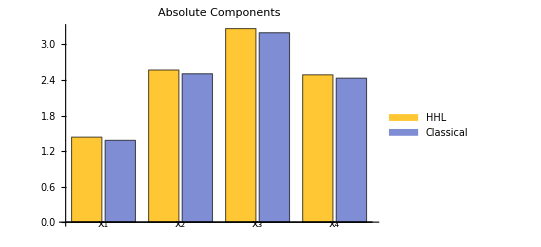

```mathematica
BarChart[Transpose@{xquantum,xclassical},PlotLabel->"Absolute Components",ChartLegends->{"HHL","Classical"},ChartLabels->{Table[Subscript[x, n],{n,4}],None}]
```

Compare the residuals from this small HHL circuit to the classical numerical error:

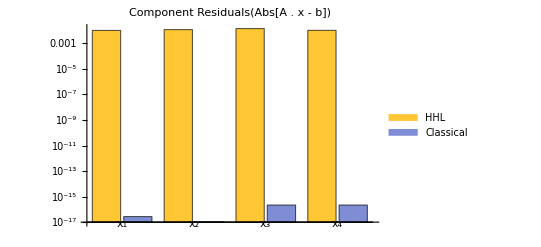

```mathematica
BarChart[Transpose@Table[Abs[Amat.v-bvec],{v,{xquantum,xclassical}}],ScalingFunctions->"Log",PlotLabel->Labeled["Component Residuals","(Abs["<>ToString[Unevaluated[A.x - b]]<>"])",Right],ChartLegends->{"HHL","Classical"},ChartLabels->{Table[Subscript[x, n],{n,4}],None}]
```

## Generalizations

The use case treated above is a canonical one, assuming the following properties:

1) The RHS vector  is normalized.
2) The matrix  is a Hermitian one.
3) The matrix  is of size .
4) The eigenvalues of  are in the range (0,1).

However, any general problem that does not follow these conditions can be resolved as follows:

1) As preprocessing, normalize , and then return the normalization factor as a post-processing.

2) Symmetrize the problem as follows:

(0 | A†
A | 0)(x
0)=(0
b)

This increases the number of qubits by 1.

3) Complete the matrix dimension to the closest  with an identity matrix. The vector  will be completed with zeros.

4) If the eigenvalues of  are in the range , you can employ transformations to the exponentiated matrix that enters into the Hamiltonian simulation, and then undo them for extracting the results:

The eigenvalues of this matrix lie in the interval [0,1) and are related to the eigenvalues of the original matrix via

with  being an eigenvalue of  resulting from the QPE algorithm. This relation between eigenvalues is then used for the expression inserted into the eigenvalue inversion, via the AmplitudeLoading function.

## Welcome to the Jungle of HHL—Rabbits vs. Foxes

The Lanchester model is widely used to describe the dynamics of combat between two opposing forces. Originally formulated for military applications, this model can also be adapted to other contexts, such as ecological competition between two species or market competition between two businesses. The model uses linear differential equations to capture the interactions between the populations, making it suitable for various scenarios where interaction terms are purely linear. In this notebook, we will explore solving this modified Lanchester model using the Harrow–Hassidim–Lloyd (HHL) algorithm, a quantum algorithm designed for efficiently solving linear systems of equations.

## Introduction to the Lanchester Model

Last sentence: can you use another word for “describe” to avoid repetition?
Mads: revised

The Lanchester Model is described in this link. The behavior of two forces, x and y, is described with the following differential equation:

where the coefficients described in the next sections represent the sensitivity of each side to the other side and to itself.

### Describe the Classical Model Using the Finite Difference Method

Assuming b=0, f=0:

First sample is simply the initial condition:

Then, for any next point, we solve numerically using the previous point:

## Building the Matrix

import numpy as np


def diff_eq_model(a, b, c0, d, e, f, g, h, dt, N, x0, y0):
    assert b==0, "please set b parameter to zero"
    assert f==0, "please set f parameter to zero"
    
    A = np.identity(2*N)

    for r in range(2*N):
        if 1<=r<=N-1:
            c=r-1
            A[r][c] = -(dt*a+1)
            c=N+r-1
            A[r][c] = -dt*c0
        elif N+1<=r:
            c=r-1
            A[r][c] = -(dt*e+1)
            c=r-1-N
            A[r][c] = -dt*g

    b1 = np.ones((N, 1))*dt*d
    b1[0] = x0
    b2 = np.ones((N, 1))*dt*h
    b2[0] = y0
    b = np.concatenate([b1,b2])

    return A,b

ExternalFunction[…]

Let’s choose some specific values for the matrix, representing a predator-prey system. Here,  represents the prey population (e.g. rabbits), and  represents the predator population (e.g. foxes). The coefficients will have the following meanings and specific values:

•  and  define the rate of natural losses or birth (due to death, disease, etc.).
  • For example,  (1% natural death rate for rabbits),  (2% natural death rate for foxes).

•  and  define the rate of losses due to environmental factors (affecting both species).
  • For example, ,  (assuming no such environmental exposure for simplicity).

•  and  are losses or gains due to interactions between species (prey being hunted by predators and vice versa).
  • For example,  (10% loss of rabbits due to predation),  (20% increase in predator population due to hunting prey).

•  and  are gains due to migration.
  • For example,  (0.4 KRabbits/year migration rate for rabbits),  (0.01 KFoxes/year migration rate for foxes).

Define the parameters:

```mathematica
rfparams={a->-0.01,b->0,c->-0.1,d->0.4,e->-0.02,f->0,g->0.02,h->0.01,x0->30,y0->1,n->8,dt->6};
```

Use the previously defined ExternalFunction:

```mathematica
{Arf,brf}=Normal@Apply[ExternalEvaluate[session,"diff_eq_model"],{a,b,c,d,e,f,g,h,dt,n,x0,y0}/.rfparams];
```

Plot the end result:

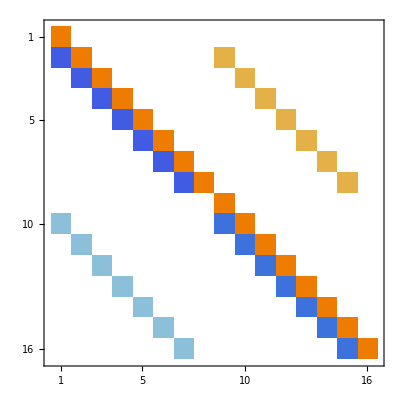
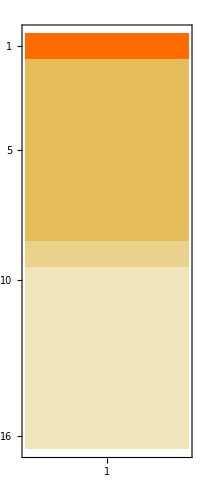

```mathematica
MatrixPlot/@{Arf,brf}
```

This accomplishes the same from an external language cell:

N=8 # N time steps
dt=6 # Sample every dt years

A,b=diff_eq_model(a=-0.01, b=0, c0=-0.1, d=0.4, e=-0.02, f=0, g=0.02, h=0.01, dt=dt, N=N, x0=30, y0=1)

[A,b]

{NumericArray[…],NumericArray[…]}

## Classical Solution

### Using NDSolve

Set up the equations:

```mathematica
rabbitfox={x'[t]==a x[t]+b x[t]y[t]+c y[t]+d,y'[t]==e y[t]+f x[t]y[t]+g x[t]+h,x[0]==x0,y[0]==y0}/.rfparams
```

{x'[t]==0.4-0.01 x[t]-0.1 y[t],y'[t]==0.01+0.02 x[t]-0.02 y[t],x[0]==30,y[0]==1}

Solve the equations:

```mathematica
{xclass,yclass}=NDSolveValue[rabbitfox,{x,y},{t,0,42}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

Visualize the result:

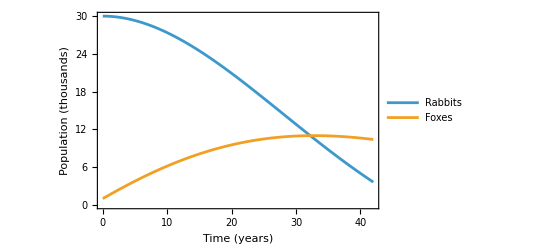

```mathematica
Plot[{xclass[t],yclass[t]},{t,0,42},
PlotLegends->{"Rabbits","Foxes"},Frame->True,FrameLabel->{"Time (years)","Population (thousands)"}]
```

Notice that at some critical point, rabbit population is so low that fox population also starts to decrease. This is a typical predator-prey model behavior.

### Via Finite Difference

Apply the finite difference method:

```mathematica
{xfd,yfd}=TakeDrop[Flatten@LinearSolve[Arf,brf],Length@brf/2]
```

{{30.,30.,27.876,24.0103,18.8847,13.032,6.98921,1.25395},{1.,4.54,7.6552,10.1417,11.8659,12.7682,12.8598,12.2154}}

```mathematica
times=Apply[Range,{0,(n-1)*dt,dt}/.rfparams]
```

{0,6,12,18,24,30,36,42}

Compare the (small n) finite difference solution to the ground truth numerical solution:

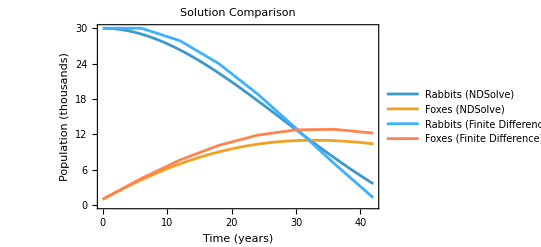

```mathematica
Show[
Plot[{xclass[t],yclass[t]},{t,0,42},
PlotLegends->{"Rabbits (NDSolve)","Foxes (NDSolve)"},Frame->True,FrameLabel->{"Time (years)","Population (thousands)"}],
ListLinePlot[Transpose/@{{times,xfd},{times,yfd}},PlotStyle->96,PlotLegends->{"Rabbits (Finite Difference)","Foxes (Finite Difference)"}],PlotLabel->"Solution Comparison"
]
```

The classical finite difference solution tracks the numerical solution with the same general shape for .

## Redefining the Matrix for HHL

Cell won’t divide.
Mads: revised

The matrix of HHL is a canonical one, assuming the following properties:

1) The RHS vector  is normalized.
2) The matrix  is a Hermitian one.
3) The matrix  is of size .
4) The eigenvalues of  are in the range (0,1).

However, any general problem that does not follow these conditions can be resolved as follows.

### Normalized Vector

As preprocessing, normalize b⃗ and then return the normalization factor as a post-processing.

norm_factor = np.linalg.norm(b)

b_normalized = b / norm_factor

### Hermitian Matrix

Symmetrize the problem as follows:

(0 | A†
A | 0)(x
0)=(0
b)

This increases the number of qubits by 1:

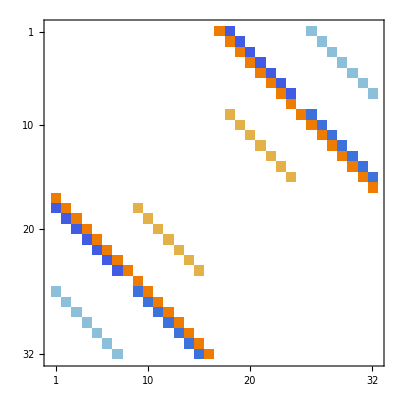

```mathematica
Apad=ArrayFlatten[{{0,ConjugateTranspose[Arf]},{Arf,0}}];
MatrixPlot[Apad]
```

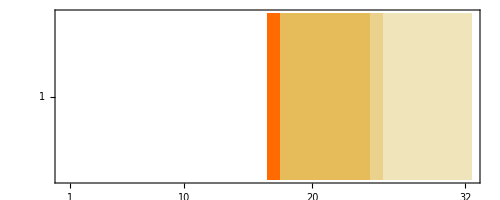

```mathematica
bpad=Join[ConstantArray[0,Length@brf],Normalize[Flatten@brf]];
MatrixPlot[{bpad}]
```

Reproducing the same matrix transformation in Python:

def to_hermitian(A):
    N = A.shape[0]
    A_hermitian = np.concatenate(
        [np.concatenate([np.zeros((N, N)), A.transpose().conj()], axis=1),
         np.concatenate([A, np.zeros((N, N))], axis=1)]
    )
    return A_hermitian

b_new = np.concatenate([np.zeros((2*N,1)), b_normalized])
#plt.matshow(b_new.transpose())
#plt.title('Normalized and Padded Vector b')
#plt.show()

A_hermitian = to_hermitian(A)

You can optionally show the result that way as well:

import matplotlib.pyplot as plt

plt.matshow(A_hermitian)
plt.title('Hermitian Matrix A')
plt.show()

### Matrix of Size 2^n×2^n

Complete the matrix dimension to the closest  with an identity matrix. The vector  will be completed with zeros:

However, our matrix is already the right size.

### Rescaled Matrix

If the eigenvalues of  are in the range , you can employ transformations to the exponentiated matrix and then undo them to extract the results:

The eigenvalues of this matrix lie in the interval [0,1) and are related to the eigenvalues of the original matrix via

with  being an eigenvalue of  resulting from the QPE algorithm. This relation between eigenvalues is then used for the expression inserted into the eigenvalue inversion, via the AmplitudeLoading function:

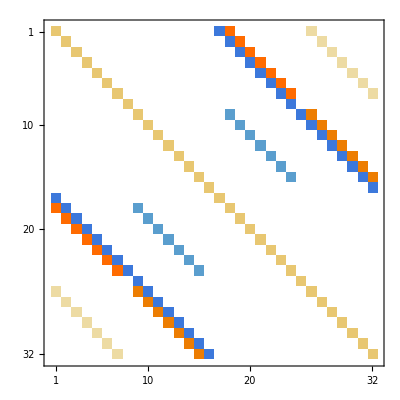

```mathematica
Ascaled=With[{λs=Eigenvalues[Apad]},
(Apad-λs[[-1]]IdentityMatrix[Length@λs])(1-2^-6)(λs[[1]]-λs[[-1]])^-1
];
MatrixPlot[Ascaled]
```

Check the matrix is Hermitian:

```mathematica
HermitianMatrixQ[Ascaled]
```

True

condition on->condition of?
Mads: on is correct

Check the condition on eigenvalues:

```mathematica
AllTrue[Eigenvalues[Ascaled],λ|->0<Abs[λ]<=1-2^-6]
```

True

Equivalently in Python:

def condition_number(A):
    w, _ = np.linalg.eig(A)
    return max(np.abs(w)) / min(np.abs(w))

QPE_RESOLUTION_SIZE = 6

assert QPE_RESOLUTION_SIZE>np.log2(condition_number(A)), "condition number is too big, and QPE resolution can not hold all eigenvalues"

w, v = np.linalg.eig(A_hermitian)
w_max=np.max(w)
w_min=np.min(w)
mat_shift=-w_min
mat_rescaling = (1 - 1 / 2 ** QPE_RESOLUTION_SIZE) / (
    w_max-w_min
)  # assures eigenvalues in [0,1-1/2^QPE_SIZE]
min_possible_w = (w_max-w_min)/2 ** QPE_RESOLUTION_SIZE # this is the minimal eigenvalue which can be resolved by the QPE

A_rescaled = (A_hermitian + mat_shift * np.identity(A_hermitian.shape[0])) * mat_rescaling

# verifying that the matrix is symmetric and has eigenvalues in [0,1)
if not np.allclose(A_rescaled, A_rescaled.T, rtol=1e-6, atol=1e-6):
    raise Exception("The matrix is not symmetric")

w_rescaled, _ = np.linalg.eig(A_rescaled)

for lam in w_rescaled:
    if lam < -1e-6 or lam >= 1:
        raise Exception("Eigenvalues are not in (0,1)")

Optionally, plot the same thing:

plt.matshow(A_rescaled)
plt.title('Rescaled Matrix A')
plt.show()

## Defining HHL Algorithm for the Quantum Solution

The two links go to the same target.
The cell won’t divide.
Mads: revised

Based on Classiq HHL in the User Guide here.

Notice the rescaling in simple_eig_inv based on the matrix rescaling:

from classiq import *

@qfunc
def simple_eig_inv(
    gamma: float,
    delta: float,
    c_param: float,
    phase: QNum,
    indicator: Output[QBit],
):
    allocate(indicator)
    assign_amplitude_table(
        lookup_table(lambda p: np.clip(c_param / ((gamma * p) + delta), -1, 1), phase),
        phase,
        indicator,
    )

ExternalFunction[…]

sol_classical_hermitian = np.array([s[0] for s in np.linalg.solve(A_hermitian, b_new)])
compared_sol = sol_classical_hermitian * min_possible_w
amp_compared = compared_sol / np.linalg.norm(compared_sol)

Besides HHL, we also perform a swap test as in the user guide, comparing the HHL solution to a state preparation of the known solution:

import scipy

exponentiation_A_rescaled = scipy.linalg.expm(1j * 2 * np.pi * A_rescaled).tolist()
b_list = np.concatenate(b_new).tolist()
amp_compared_list = amp_compared.tolist()

@qfunc
def main(indicator: Output[QBit], test: Output[QBit]) -> None:
    state = QArray("state")
    compared_state = QArray("compared_state")
    rescaled_eig = QNum("rescaled_eig")
    allocate(QPE_RESOLUTION_SIZE, UNSIGNED, QPE_RESOLUTION_SIZE, rescaled_eig)
    prepare_amplitudes(b_list, 0, state)
    within_apply(
        lambda: qpe(
            unitary=lambda: unitary(exponentiation_A_rescaled, state),
            phase=rescaled_eig,
        ),
        lambda: simple_eig_inv(
            gamma=mat_rescaling ** (-1),
            delta=-mat_shift,
            c_param=min_possible_w,
            phase=rescaled_eig,
            indicator=indicator,
        ),
    )
    prepare_amplitudes(amp_compared_list, 0.0, compared_state)
    swap_test(state, compared_state, test)
    
    drop(rescaled_eig)
    drop(state)
    drop(compared_state)

ExternalFunction[…]

We will create the circuit with depth limitation compared to the maximal width in a simulator (25). We also set the preferences for synthesis and execution:

constraints = Constraints(
    max_width=25,
    # optimization_parameter=OptimizationParameter.DEPTH,
)
preferences = Preferences(
    optimization_level=0, optimization_timeout_seconds=90, transpilation_option="none"
)
NUM_SHOTS = 2048
execution_preferences = ExecutionPreferences(num_shots=NUM_SHOTS)

qmod_hhl_swap_test = create_model(main, constraints, execution_preferences, preferences)

## Synthesize and Show

For a circuit like this one, the synthesis step may take longer than the previous examples:

qprog_hhl_swap = synthesize(qmod_hhl_swap_test)
show(qprog_hhl_swap)

Quantum program link: https://platform.classiq.io/circuit/36wp62LPGBytKLJkScI1dAtwbVo

-Graphics-

## Execution and Results Analysis

As explained in the swap test user guide.

Comparing the measured overlap with the exact overlap done using the expected probability of measuring the state  as defined as:

we extract the overlap . The exact overlap is computed with the dot product of the two state vectors. Note that for the sake of this demonstration, we execute this circuit 100,000 times to improve the precision of the probability estimate. This is usually not required in actual programs.

Since we are in HHL context, we filter only the indicator==1 results:

swap_test_job = execute(qprog_hhl_swap)

results = swap_test_job.result()
histogram = results[0].value
fidelity_basic = np.sqrt(
    histogram.counts_of_multiple_outputs(["indicator", "test"])[("1", "0")]
    * 2
    / (histogram.counts_of_output("indicator")["1"])
    - 1
)

print("Fidelity between basic HHL and classical solutions:", fidelity_basic)

Fidelity between basic HHL and classical solutions: 0.982299486257503

swap_test_job.open_in_ide()

-Graphics-

## State Vector Simulation

We can also run the statevector of the HHL result and examine it, without a swap test. Extracting the full information is exponentially hard and used here just for educational purposes. Extension of this work can extract some information from the statevector, like the last element, which is the most important one. We can also pad with extension of the last solution and therefore measure the last point in high probability:

class TimeIndexAndGroup(QStruct):
    rabbits: QBit
    time_index: QNum


@qfunc
def main(
    indicator: Output[QBit],
    time_index_and_group: Output[TimeIndexAndGroup],
    rescaled_eig: Output[QNum],
) -> None:
    allocate(QPE_RESOLUTION_SIZE, False, QPE_RESOLUTION_SIZE, rescaled_eig)
    prepare_amplitudes(b_list, 0, time_index_and_group)
    within_apply(
        lambda: qpe(
            unitary=lambda: unitary(exponentiation_A_rescaled, time_index_and_group),
            phase=rescaled_eig,
        ),
        lambda: simple_eig_inv(
            gamma=mat_rescaling ** (-1),
            delta=-mat_shift,
            c_param=min_possible_w,
            phase=rescaled_eig,
            indicator=indicator,
        ),
    )


MAX_WIDTH_BASIC = 18
constraints = Constraints(max_width=MAX_WIDTH_BASIC)
preferences = Preferences(
    optimization_level=0, optimization_timeout_seconds=90, transpilation_option="none"
)
backend_preferences = ClassiqBackendPreferences(
    backend_name=ClassiqSimulatorBackendNames.SIMULATOR_STATEVECTOR
)
execution_preferences = ExecutionPreferences(
    num_shots=1, backend_preferences=backend_preferences
)

qmod_hhl_basic = create_model(
    main,
    constraints=constraints,
    preferences=preferences,
    execution_preferences=execution_preferences,
)
write_qmod(qmod_hhl_basic, "hhl_lanchester", decimal_precision=12, symbolic_only=False)
qprog_hhl_basic = synthesize(qmod_hhl_basic)
show(qprog_hhl_basic)

Quantum program link: https://platform.classiq.io/circuit/36wpMBDfGRk9nVqO1p4KGHiSO30

-Graphics-

job_hhl_basic = execute(qprog_hhl_basic)
results = job_hhl_basic.result()
statevector = results[0].value.state_vector
job_hhl_basic.open_in_ide()

We should filter the results, extract the amplitudes of the statevector and compare them to the classical solution. We filter only the indicator=1 and phase=0 results:

filtered_hhl_statevector =dict()
for sample in results[0].value.parsed_state_vector:
    if sample.state["indicator"]==1 and sample.state["rescaled_eig"]==0:
        filtered_hhl_statevector[sample.state["time_index_and_group"]] = sample.amplitude

states = list(filtered_hhl_statevector.keys())
states.sort()
raw_qsol = np.array([filtered_hhl_statevector[s] for s in states])

Save the raw solution and compare the Hermitian matrix with the classical one:

qsol_hermitian  = raw_qsol / (min_possible_w)

Now we can compare the two solutions in the time domain, after putting back the normalization factor:

```mathematica
With[
{qsol=Chop@Normal@ExternalEvaluate[session,"qsol_hermitian"],
len=n/.rfparams,
norm=ExternalEvaluate[session,"norm_factor"]},
{xhhl,yhhl}=norm{qsol[[1;;len]],qsol[[1+len;;2*len]]}
]
```

{{30.0284,30.3686,28.3026,24.4755,19.2582,13.1725,6.83454,0.569269},{0.912559,4.44077,7.72408,10.4227,12.2733,13.3856,13.6333,12.9233}}

Visualize the quantum HHL solution, the classical finite difference solution and the ground truth numerical solution all together:

The last label should end with a close parenthesis: Foxes (HHL)
Mads: revised

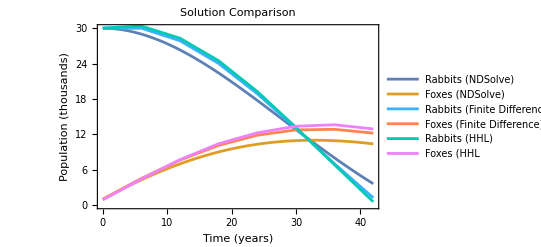

The fidelity of the statevector solution can be compared with the fidelity of the classical finite difference solution:

```mathematica
Module[
{
hhlsol=Flatten@{xhhl,yhhl},
fdsol=Flatten@{xfd,yfd},
gt=Flatten@Transpose@Table[{xclass[t],yclass[t]},{t,times}],
fidelity=((1-CosineDistance[#1,#2])^2&),
ds
},
ds=Dataset[<|"Classical Finite Difference (N=8)"-><|"Fidelity (vs NDSolve)"->fidelity[fdsol,gt]|>,"Quantum HHL (N=8)"-><|"Fidelity (vs NDSolve)"->fidelity[hhlsol,gt]|>|>];
Rasterize@ds[All,All,PercentForm]
]
```

-Graphics-

The statevector solution has high fidelity with the classical finite difference solution as well:

fidelity = (
    np.abs(
        np.dot(
            sol_classical_hermitian / np.linalg.norm(sol_classical_hermitian),
            qsol_hermitian / np.linalg.norm(qsol_hermitian),
        )
    )
    ** 2
)
print("Statevector Solution Fidelity:", fidelity)

Statevector Solution Fidelity: 0.9996462667876238

## Summary

This notebook demonstrated the implementation of the HHL algorithm on a structured, real-world system—the Lanchester predator-prey model.

Beginning with a pair of coupled differential equations, we reformulated the model into a linear system using the finite difference method and then performed a series of transformations to prepare it for HHL: normalization of the RHS vector, Hermitian matrix embedding and eigenvalue rescaling. Leveraging Classiq’s synthesis tools and statevector simulation, we built and executed the quantum circuit, extracting the encoded solution with high accuracy.

The quantum result was benchmarked against both a classical finite difference solution and Mathematica’s `NDSolve`, achieving a fidelity above 99%.

These results reinforce the HHL algorithm’s ability to handle realistic differential equation models and lay the groundwork for scalable quantum simulation in scientific domains.

Practical Challenges and Limitations

Despite the successful implementation of HHL in this notebook, realizing a practical quantum advantage for solving linear systems remains elusive.

The core challenges stem from the overhead of satisfying HHL’s input requirements: transforming a generic matrix into a Hermitian one, rescaling eigenvalues to a narrow interval and normalizing the RHS vector all introduce classical preprocessing steps that can be computationally expensive.

Additionally, the circuit depth grows significantly with the desired precision and the matrix condition number—often exceeding what current quantum hardware can handle.

Post-processing the quantum output (e.g. via swap tests or filtering statevector amplitudes) also involves additional classical effort and often cannot return the full solution vector efficiently.

Consequently, while HHL is a foundational algorithm that demonstrates the power of quantum linear solvers in theory, in practice its application to real-world problems—such as ecological or financial modeling—remains limited by current technological and algorithmic constraints.